```mathematica
filesAR=FileNames["/home/carla/GDC/CONF/MUR/GDC_Conf_AR_MUR_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/CONF/MUR/GDC_Conf_BR_MUR_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]]
confBR=dataBR[[All,1]]
```

{{{0.00642674,5,778},{0.0053424,0.00642674,0.00109016},{0.711271,0.00642674,0.0000311817,0.00109016}},{{0.00642674,5,778},{0.00540125,0.00642674,0.00103105},{0.724784,0.00642674,5.8913×10^-6,0.00103105}},{{0.0625,1,16},{0.0614515,0.0625,0.00111718},{0.967001,0.0625,7.04179×10^-8,0.00111718}},{{0.0625,1,16},{0.0614909,0.0625,0.0010752},{0.968222,0.0625,3.43271×10^-9,0.0010752}},{{0.00884956,1,113},{0.00729984,0.00884956,0.00156111},{0.701957,0.00884956,1.62483×10^-9,0.00156111}},{{0.0232558,1,43},{0.0229213,0.0232558,0.000342354},{0.97164,0.0232558,6.29454×10^-11,0.000342354}},{{1.,1,1},{1.,1.,0.000451474},{1,1.,2.14577×10^-13,0.000451474}},{{1.,1,1},{1.,1.,0.000435964},{1,1.,9.9865×10^-14,0.000435964}}}

{{{0.00642674,40,6224},{0.00540125,0.00642674,0.00103105},{0.724784,0.00642674,0.0000471304,0.00103105}},{{0.0042735,5,1170},{0.00328668,0.0042735,0.000990076},{0.624806,0.0042735,5.14931×10^-6,0.000990076}},{{0.0625,3,48},{0.0614909,0.0625,0.0010752},{0.968222,0.0625,1.02981×10^-8,0.0010752}},{{0.0232558,1,43},{0.0226576,0.0232558,0.000612063},{0.949845,0.0232558,6.18298×10^-10,0.000612063}},{{0.00487805,5,1025},{0.00304249,0.00487805,0.00184116},{0.453182,0.00487805,1.50044×10^-9,0.00184116}},{{0.0232558,1,43},{0.0229253,0.0232558,0.000338286},{0.971973,0.0232558,9.2268×10^-12,0.000338286}},{{1.,1,1},{1.,1.,0.000435964},{1,1.,9.9865×10^-14,0.000435964}}}

```mathematica
dojCHEVBKAR=confAR[[All,1]][[All,1]]
dojCHAR=confAR[[All,2]][[All,3]]
dojEVBKAR=confAR[[All,3]][[All,3]]

dojCHEVBKBR=confBR[[All,1]][[All,1]]
dojCHBR=confBR[[All,2]][[All,3]]
dojEVBKBR=confBR[[All,3]][[All,3]]
```

{0.00642674,0.00642674,0.0625,0.0625,0.00884956,0.0232558,1.,1.}

{0.00109016,0.00103105,0.00111718,0.0010752,0.00156111,0.000342354,0.000451474,0.000435964}

{0.0000311817,5.8913×10^-6,7.04179×10^-8,3.43271×10^-9,1.62483×10^-9,6.29454×10^-11,2.14577×10^-13,9.9865×10^-14}

{0.00642674,0.0042735,0.0625,0.0232558,0.00487805,0.0232558,1.}

{0.00103105,0.000990076,0.0010752,0.000612063,0.00184116,0.000338286,0.000435964}

{0.0000471304,5.14931×10^-6,1.02981×10^-8,6.18298×10^-10,1.50044×10^-9,9.2268×10^-12,9.9865×10^-14}

```mathematica
(*sList={"S0","S1","S2","S3","S4","S5","S6","S7","S8"};
dojP=Labeled[#[[1]],#[[2]]]&/@Map[{doj[[#]],sList[[#]]}&,ran]*)

sList={1,2,3,4,5,6,7,8};
sList2={1.5,2.5,3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojAAR={#[[2]],#[[1]]}&/@Map[{N[dojCHAR[[#]]/dojCHEVBKAR[[#]]],sList[[#]]}&,ran]
dojABR={#[[2]],#[[1]]}&/@Map[{N[dojCHBR[[#]]/dojCHEVBKBR[[#]]],sList2[[#]]}&,ran2]
dojPCHAR={#[[2]],#[[1]]}&/@Map[{dojCHAR[[#]],sList[[#]]}&,ran]
dojPCHBR={#[[2]],#[[1]]}&/@Map[{dojCHBR[[#]],sList2[[#]]}&,ran2]
dojPEVBKAR={#[[2]],#[[1]]}&/@Map[{dojEVBKAR[[#]],sList[[#]]}&,ran]
dojPEVBKBR={#[[2]],#[[1]]}&/@Map[{dojEVBKBR[[#]],sList2[[#]]}&,ran2]
```

{{1,0.169628},{2,0.160432},{3,0.0178749},{4,0.0172032},{5,0.176406},{6,0.0147212},{7,0.000451474},{8,0.000435964}}

{{1.5,0.160432},{2.5,0.231678},{3.5,0.0172032},{4.5,0.0263187},{5.5,0.377438},{6.5,0.0145463},{7.5,0.000435964}}

{{1,0.00109016},{2,0.00103105},{3,0.00111718},{4,0.0010752},{5,0.00156111},{6,0.000342354},{7,0.000451474},{8,0.000435964}}

{{1.5,0.00103105},{2.5,0.000990076},{3.5,0.0010752},{4.5,0.000612063},{5.5,0.00184116},{6.5,0.000338286},{7.5,0.000435964}}

{{1,0.0000311817},{2,5.8913×10^-6},{3,7.04179×10^-8},{4,3.43271×10^-9},{5,1.62483×10^-9},{6,6.29454×10^-11},{7,2.14577×10^-13},{8,9.9865×10^-14}}

{{1.5,0.0000471304},{2.5,5.14931×10^-6},{3.5,1.02981×10^-8},{4.5,6.18298×10^-10},{5.5,1.50044×10^-9},{6.5,9.2268×10^-12},{7.5,9.9865×10^-14}}

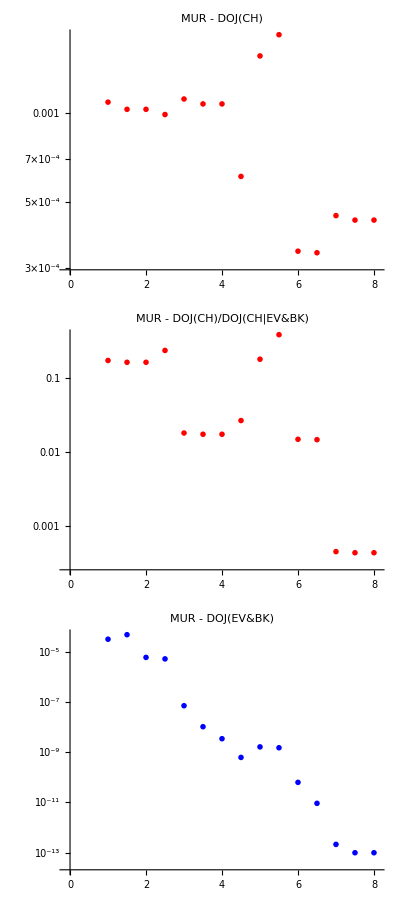

```mathematica
aPlot=ListLogPlot[{Union[dojAAR,dojABR]},  PlotLabel->"MUR - DOJ(CH)/DOJ(CH|EV&BK)", PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red}, PlotRange->All, PlotMarkers->{{"A",12}},ImageSize->400];
chPlot=ListLogPlot[{Union[dojPCHAR,dojPCHBR]}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red}, PlotRange->All, PlotLabel->"MUR - DOJ(CH)", PlotMarkers->{{"C",12}},ImageSize->400];
evbkPlot=ListLogPlot[{Union[dojPEVBKAR,dojPEVBKBR]},PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Blue}, PlotRange->All, PlotLabel->"MUR - DOJ(EV&BK)", PlotMarkers->{{"E",12}},ImageSize->400];
allPlot=ListLogPlot[{Union[dojPCHAR,dojPCHBR], Union[dojPEVBKAR,dojPEVBKBR]}, PlotLegends->{"DOJ(CH)","DOJ(EV&BK)"}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red, Blue}, PlotRange->All, PlotLabel->"MUR - DOJ(CH),DOJ(EV&BK)", PlotMarkers->{{"C",12},{"E",12}},ImageSize->400];
plotsOut=Column[{chPlot,aPlot,evbkPlot}, ItemSize->35, Alignment->Center]
```

```mathematica
SetDirectory["/home/carla/GDC/CONF/MUR/"];
Export["MUR_CH_EVBK.jpeg",plotsOut,ImageResolution->200]
Put[Union[dojPCHAR,dojPCHBR],"MUR_Z_APP.txt"]
Put[Union[dojAAR,dojABR],"MUR_F_APP.txt"]
```

MUR_CH_EVBK.jpeg

```mathematica
(*PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{0, 0.026},  PlotLabel->"MUR - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
Export["MUR_Zoomed_In.jpeg",PlotParts,ImageSize->850]*)
```